-Graphics- |   Métodos Computacionales en Álgebra para Informáticos
Matemática Discreta y Lógica
Dpto. de Matemáticas. Área de  Álgebra  (M. A. García, C. Ordóñez, J. F. Ruiz)

# Capítulo 9 Retículos y álgebras de Boole finitas

## 1. Retículos

### Ejemplo 9.1.

Determinar si el conjunto ordenado del ejemplo 8.8. es un retículo.

Utilizamos la función 9.1.:

```mathematica
RETICULO[A_,R_]:=Module[{reticulo,cotassuperiores,cotasinferiores,csuper,cinfer,supremo,infimo,mini,maxi,n,m,x1,x2},reticulo=True;
Do[Do[cotassuperiores={};cotasinferiores={};
Do[csuper=True;cinfer=True;
If[Intersection[{{A[[x1]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[x2]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[n]],A[[x1]]}},R]=={},cinfer=False];
If[Intersection[{{A[[n]],A[[x2]]}},R]=={},cinfer=False];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};infimo={};
Do[mini=True;
Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];
If[supremo=={},reticulo=False];
Do[maxi=True;
Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];
         ,{n,1,Length[cotasinferiores]}];
If[infimo=={},reticulo=False];
      ,{x1,1,Length[A]}];
   ,{x2,1,Length[A]}];
reticulo
]
```

```mathematica
A={a,b,c,d,e,f,g,h,i};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
```

```mathematica
RETICULO[A,R]
```

False

Por tanto, no es un retículo.

### Ejemplo 9.2.

Comprobar que el conjunto ordenado cuyo diagrama de Hasse es el de la ilustración 9.2. es un retículo.

```mathematica
RETICULO[A_,R_]:=Module[{reticulo,cotassuperiores,cotasinferiores,csuper,cinfer,supremo,infimo,mini,maxi,n,m,x1,x2},reticulo=True;
Do[Do[cotassuperiores={};cotasinferiores={};
Do[csuper=True;cinfer=True;
If[Intersection[{{A[[x1]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[x2]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[n]],A[[x1]]}},R]=={},cinfer=False];
If[Intersection[{{A[[n]],A[[x2]]}},R]=={},cinfer=False];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};infimo={};
Do[mini=True;
Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];
If[supremo=={},reticulo=False];
Do[maxi=True;
Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];
         ,{n,1,Length[cotasinferiores]}];
If[infimo=={},reticulo=False];
      ,{x1,1,Length[A]}];
   ,{x2,1,Length[A]}];
reticulo
]
```

```mathematica
A={a,b,c,d,e,f};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{b,b},{b,f},{c,c},{c,e},{c,f},{d,d},{d,f},{e,e},{e,f},{f,f}};
```

```mathematica
RETICULO[A,R]
```

True

Luego, en este caso si es un retículo.

### Ejemplo 9.3.

Calcular las tablas de operaciones del retículo del ejemplo 9.2.

En primer lugar introducimos las funciones SUPREMO[] e INFIMO[] (8.10. y 8.12. respectivamente).

```mathematica
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},
cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};
Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];
supremo
]
```

```mathematica
INFIMO[A_,B_,R_]:=Module[{cotasinferiores,cinfer,infimo,maxi,n,m},
cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
infimo={};
Do[maxi=True;
Do[If[MemberQ[R,{cotasinferiores[[m]],cotasinferiores[[n]]}],,maxi=False;Break[];],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]];Break[];];,{n,1,Length[cotasinferiores]}];
infimo
]
```

Ejecutando el programa 9.1. obtenemos:

```mathematica
A={a,b,c,d,e,f};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{b,b},{b,f},{c,c},{c,e},{c,f},{d,d},{d,f},{e,e},{e,f},{f,f}};
n=Length[A];
TABLASUP=Table[0,{i,n},{j,n}];
TABLAINF=Table[0,{i,n},{j,n}];
Do[
Do[
TABLASUP[[i,j ]]=SUPREMO[A,{A[[i]],A[[j]]},R];
TABLAINF[[i,j]]=INFIMO[A,{A[[i]],A[[j]]},R],
{i,n}],
{j,n}]
Print["Tabla operación supremo:"]
TableForm[TABLASUP,TableHeadings->{A,A}]
Print["Tabla operación ínfimo:"]
TableForm[TABLAINF,TableHeadings->{A,A}]
```

Tabla operación supremo:

| a | b | c | d | e | f
a | a | b | c | d | e | f
b | b | b | f | f | f | f
c | c | f | c | f | e | f
d | d | f | f | d | f | f
e | e | f | e | f | e | f
f | f | f | f | f | f | f

Tabla operación ínfimo:

| a | b | c | d | e | f
a | a | a | a | a | a | a
b | a | b | a | a | a | b
c | a | a | c | a | c | c
d | a | a | a | d | a | d
e | a | a | c | a | e | e
f | a | b | c | d | e | f

### Ejemplo 9.4.

En el conjunto A de los divisores positivos de 88 definimos las siguientes leyes de composición
a  ∧  b = m.c.d.{a, b}   y  a ∨ b = m.c.m.{a, b} (ver capítulo 10).
	Comprobamos que ambas operaciones satisfacen las propiedades de absorción y de idempotencia. De igual forma se podría comprobar que satisfacen conmutativas y asociativas, por lo que podríamos concluir que la terna (D,  ∧,  ∨) es un retículo.

Primero calculamos los divisores positivos de 88:

```mathematica
A=Divisors[88]
```

{1,2,4,8,11,22,44,88}

e introducimos las operaciones:

```mathematica
op[a_,b_]:=GCD[a,b];
oq[a_,b_]:=LCM[a,b];
```

Ejecutando el programa 9.2. para comprobar si satisface la absorción:

```mathematica
absorcion=True;
CONTADORi=1;
While[absorcion&&CONTADORi≤Length[A],CONTADORj=1;
While[absorcion&&CONTADORj≤Length[A],If[TrueQ[oq[op[A[[CONTADORi]],A[[CONTADORj]]],A[[CONTADORi]]]==A[[CONTADORi]]]&&TrueQ[op[oq[A[[CONTADORi]],A[[CONTADORj]]],A[[CONTADORi]]]==A[[CONTADORi]]], ,absorcion=False];
CONTADORj++;];CONTADORi++;];
absorcion
```

True

Y de igual forma el programa 9.3. para comprobar la idempotencia :

```mathematica
idempotencia=True;
CONTADORi=1;
While[idempotencia&&CONTADORi≤Length[A],If[TrueQ[op[A[[CONTADORi]],A[[CONTADORi]]]==A[[CONTADORi]]]&&TrueQ[oq[A[[CONTADORi]],A[[CONTADORi]]]==A[[CONTADORi]]], ,idempotencia=False];CONTADORi++;];
idempotencia
```

True

## 2. Tipos de retículos

### 2.1. Retículos con elementos 0 y 1

### Ejemplo 9.5.

Sea A = {a, b, c, d, e} y R = {(a, a), (a, b), (a, c), (a, d), (a, e), (b, b), (b, c), (b, e), (c, c), (c, e), (d, d), (d, e), (e, e)}, determinar si:
	(a)	¿Es A un conjunto ordenado? 
	(b)	¿Es A un retículo?
	(c)     ¿Es A un retículo con elemento 0 y elemento 1?

Cargamos las funciones previas que vamos a utilizar:

```mathematica
ORDEN[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

```mathematica
RETICULO[A_,R_]:=Module[{reticulo,cotassuperiores,cotasinferiores,csuper,cinfer,supremo,infimo,mini,maxi,n,m,x1,x2},reticulo=True;
Do[Do[cotassuperiores={};cotasinferiores={};
Do[csuper=True;cinfer=True;
If[Intersection[{{A[[x1]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[x2]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[n]],A[[x1]]}},R]=={},cinfer=False];
If[Intersection[{{A[[n]],A[[x2]]}},R]=={},cinfer=False];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};infimo={};
Do[mini=True;
Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];
If[supremo=={},reticulo=False];
Do[maxi=True;
Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];
         ,{n,1,Length[cotasinferiores]}];
If[infimo=={},reticulo=False];
      ,{x1,1,Length[A]}];
   ,{x2,1,Length[A]}];
reticulo
]
```

```mathematica
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},
maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales
]
```

```mathematica
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},
minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales
]
```

```mathematica
A={a,b,c,d,e};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{b,b},{b,c},{b,e},{c,c},{c,e},{d,d},{d,e},{e,e}};
ORDEN[A,R]
```

R es reflexiva

R es antisimétrica

R es transitiva

R es una relación de orden

```mathematica
RETICULO[A, R]
```

True

```mathematica
MAXIMALES[A,R]
```

{e}

```mathematica
MINIMALES[A,R]
```

{a}

Por tanto A es un retículo donde "a" es el elemento 0 y "e" es el elemento 1.

### 2.2. Retículos distributivos

### Ejemplo 9.6.

Sabemos que A = {a, b, c, d, e} con la relación de orden R = {(a, a), (a, b), (a, c), (a, d), (a, e), (b, b), (b, c), (b, e), (c, c), (c, e), (d, d), (d, e), (e, e)} es un retículo por el ejemplo anterior, comprobar si es distributivo.

Comencemos ejecutando las funciones SUPREMO e INFIMO necesarias para que funcione la nueva orden:

```mathematica
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},
cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};
Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];
supremo
]
```

```mathematica
INFIMO[A_,B_,R_]:=Module[{cotasinferiores,cinfer,infimo,maxi,n,m},
cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
infimo={};
Do[maxi=True;
Do[If[MemberQ[R,{cotasinferiores[[m]],cotasinferiores[[n]]}],,maxi=False;Break[];],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]];Break[];];,{n,1,Length[cotasinferiores]}];
infimo
]
```

Ejecutamos la orden que estudia si es retículo es distributivo:

```mathematica
RETICULODISTRIBUTIVO[A_,R_]:=Module[{distributive,i,j,k},distributivo=True;
Do[Do[Do[If[TrueQ[SUPREMO[A,Union[{A[[i]]},INFIMO[A,{A[[j]],A[[k]]},R]],R]==INFIMO[A,Union[SUPREMO[A,{A[[i]],A[[j]]},R],SUPREMO[A,{A[[i]],A[[k]]},R]],R]],,distributivo=False;];         
,{i,1,Length[A]}];
      ,{j,1,Length[A]}];
   ,{k,1,Length[A]}];
distributivo
]
```

```mathematica
A={a,b,c,d,e};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{b,b},{b,c},{b,e},{c,c},{c,e},{d,d},{d,e},{e,e}};

RETICULODISTRIBUTIVO[A,R]
```

False

### Ejemplo 9.7.

Sea A = {1, 2, 3, 4} un conjunto con la relación de orden R = {(1, 1), (1, 2), (1, 3), (1, 4), (2, 2), (2, 4), (3, 3), (3, 4), (4, 4)}, comprobar que es un retículo distributivo.

```mathematica
ORDEN[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

```mathematica
RETICULO[A_,R_]:=Module[{reticulo,cotassuperiores,cotasinferiores,csuper,cinfer,supremo,infimo,mini,maxi,n,m,x1,x2},reticulo=True;
Do[Do[cotassuperiores={};cotasinferiores={};
Do[csuper=True;cinfer=True;
If[Intersection[{{A[[x1]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[x2]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[n]],A[[x1]]}},R]=={},cinfer=False];
If[Intersection[{{A[[n]],A[[x2]]}},R]=={},cinfer=False];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};infimo={};
Do[mini=True;
Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];
If[supremo=={},reticulo=False];
Do[maxi=True;
Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];
         ,{n,1,Length[cotasinferiores]}];
If[infimo=={},reticulo=False];
      ,{x1,1,Length[A]}];
   ,{x2,1,Length[A]}];
reticulo
]
```

```mathematica
RETICULODISTRIBUTIVO[A_,R_]:=Module[{distributive,i,j,k},distributivo=True;
Do[Do[Do[If[TrueQ[SUPREMO[A,Union[{A[[i]]},INFIMO[A,{A[[j]],A[[k]]},R]],R]==INFIMO[A,Union[SUPREMO[A,{A[[i]],A[[j]]},R],SUPREMO[A,{A[[i]],A[[k]]},R]],R]],,distributivo=False;];         
,{i,1,Length[A]}];
      ,{j,1,Length[A]}];
   ,{k,1,Length[A]}];
distributivo
]
```

```mathematica
A={1,2,3,4};
R={{1,1},{1,2},{1,3},{1,4},{2,2},{2,4},{3,3},{3,4},{4,4}};
ORDEN[A,R]
```

R es reflexiva

R es antisimétrica

R es transitiva

R es una relación de orden

```mathematica
RETICULO[A,R]
```

True

```mathematica
RETICULODISTRIBUTIVO[A,R]
```

True

Y en efecto comprobamos que es un retículo distributivo.

### 2.3. Retículos complementados

### Ejemplo 9.8.

Sea A = {a, b, c, d, e} con la relación de orden R = {(a, a), (a, b), (a, c), (a, d), (a, e), (b, b), (b, c), (b, e), (c, c), (c, e), (d, d), (d, e), (e, e)} que sabemos que es un retículo con elemento cero y elemento uno, pero no es distributivo. Calcular, si existe, el complemento o complementos del elemento d.

Primero ejecutamos la función 9.4.:

```mathematica
COMPLEMENTO[A_,R_,n_]:=Module[{complemento,k},complemento={};
Do[If[INFIMO[A,{A[[k]],n},R]==MINIMALES[A,R]&&SUPREMO[A,{A[[k]],n},R]==MAXIMALES[A,R],AppendTo[complemento,A[[k]]]],{k,1,Length[A]}];
complemento]
```

```mathematica
A={a,b,c,d,e};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{b,b},{b,c},{b,e},{c,c},{c,e},{d,d},{d,e},{e,e}};
COMPLEMENTO[A,R,d]
```

{b,c}

### Ejemplo 9.9.

Comprobar que el conjunto ordenado mostrado en la ilustración 9.6. es un retículo en el cual el elemento y (en rojo en la ilustración) no tiene complemento:

Primero ejecutamos la función 9.4.:

```mathematica
COMPLEMENTO[A_,R_,n_]:=Module[{complemento,k},complemento={};
Do[If[INFIMO[A,{A[[k]],n},R]==MINIMALES[A,R]&&SUPREMO[A,{A[[k]],n},R]==MAXIMALES[A,R],AppendTo[complemento,A[[k]]]],{k,1,Length[A]}];
complemento]
```

```mathematica
A={x,y,z,t};
R={{x,x},{x,y},{x,z},{x,t},{y,y},{y,z},{y,t},{z,z},{z,t},{t,t}};
COMPLEMENTO[A,R,y]
```

{}

### Ejemplo 9.10.

Comprobar si el retículo del ejercicio 9.4. es complementado (ver ilustración 9.3.).

Primero ejecutamos la función 9.5.:

```mathematica
COMPLEMENTADO[A_,R_]:=Module[{complementado,k},complementado=True;
Do[If[COMPLEMENTO[A,R,A[[k]]]=={},complementado=False],{k,1,Length[A]}];
complementado]
```

```mathematica
A={a,b,c,d,e};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{b,b},{b,d},{b,e},{c,c},{c,e},{d,d},{d,e},{e,e}};
COMPLEMENTADO[A,R]
```

True

## 3. Álgebras de Boole finitas

### Ejemplo 9.11.

Sea A = {a, b, c, d, e, f} y sea la relación binaria R = {(a, a), (a, b), (a, c), (a, d), (a, e), (a, f), (b, b), (b, c), (b, f), (c, c), (c, f), (d, d), (d, e), (d, f), (e, e), (e, f), (f, f)}, comprobar si R es una relación de orden y en caso afirmativo comprobar si A con R es un álgebra de Boole.

```mathematica
ORDEN[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

```mathematica
RETICULO[A_,R_]:=Module[{reticulo,cotassuperiores,cotasinferiores,csuper,cinfer,supremo,infimo,mini,maxi,n,m,x1,x2},reticulo=True;
Do[Do[cotassuperiores={};cotasinferiores={};
Do[csuper=True;cinfer=True;
If[Intersection[{{A[[x1]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[x2]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[n]],A[[x1]]}},R]=={},cinfer=False];
If[Intersection[{{A[[n]],A[[x2]]}},R]=={},cinfer=False];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};infimo={};
Do[mini=True;
Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];
If[supremo=={},reticulo=False];
Do[maxi=True;
Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];
         ,{n,1,Length[cotasinferiores]}];
If[infimo=={},reticulo=False];
      ,{x1,1,Length[A]}];
   ,{x2,1,Length[A]}];
reticulo
]
```

```mathematica
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},
maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales
]
```

```mathematica
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},
minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales
]
```

```mathematica
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},
cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};
Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];
supremo
]
```

```mathematica
INFIMO[A_,B_,R_]:=Module[{cotasinferiores,cinfer,infimo,maxi,n,m},
cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
infimo={};
Do[maxi=True;
Do[If[MemberQ[R,{cotasinferiores[[m]],cotasinferiores[[n]]}],,maxi=False;Break[];],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]];Break[];];,{n,1,Length[cotasinferiores]}];
infimo
]
```

```mathematica
RETICULODISTRIBUTIVO[A_,R_]:=Module[{distributive,i,j,k},distributivo=True;
Do[Do[Do[If[TrueQ[SUPREMO[A,Union[{A[[i]]},INFIMO[A,{A[[j]],A[[k]]},R]],R]==INFIMO[A,Union[SUPREMO[A,{A[[i]],A[[j]]},R],SUPREMO[A,{A[[i]],A[[k]]},R]],R]],,distributivo=False;];         
,{i,1,Length[A]}];
      ,{j,1,Length[A]}];
   ,{k,1,Length[A]}];
distributivo
]
```

```mathematica
COMPLEMENTADO[A_,R_]:=Module[{complementado,k},complementado=True;
Do[If[COMPLEMENTO[A,R,A[[k]]]=={},complementado=False],{k,1,Length[A]}];
complementado]
```

```mathematica
A={a,b,c,d,e,f};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{b,b},{b,c},{b,f},{c,c},{c,f},{d,d},{d,e},{d,f},{e,e},{e,f},{f,f}};
ORDEN[A,R]
```

R es reflexiva

R es antisimétrica

R es transitiva

R es una relación de orden

```mathematica
RETICULO[A,R]
```

True

```mathematica
MAXIMALES[A,R]
```

{f}

```mathematica
MINIMALES[A,R]
```

{a}

```mathematica
COMPLEMENTADO[A,R]
```

True

```mathematica
RETICULODISTRIBUTIVO[A,R]
```

False

Por tanto no es un álgebra de Boole, ya que no es un retículo distributivo aunque si es un retículo con elemento 0, elemento 1 y complementado.

### Ejemplo 9.12.

Sea A = {1, 2, 3, 4} con la relación de orden R = {(1, 1), (1, 2), (1, 3), (1, 4), (2, 2), (2, 4), (3, 3), (3, 4), (4, 4)} (ver ilustración 9.4.), comprobar si A es un álgebra de Boole.

```mathematica
RETICULO[A_,R_]:=Module[{reticulo,cotassuperiores,cotasinferiores,csuper,cinfer,supremo,infimo,mini,maxi,n,m,x1,x2},reticulo=True;
Do[Do[cotassuperiores={};cotasinferiores={};
Do[csuper=True;cinfer=True;
If[Intersection[{{A[[x1]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[x2]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[n]],A[[x1]]}},R]=={},cinfer=False];
If[Intersection[{{A[[n]],A[[x2]]}},R]=={},cinfer=False];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};infimo={};
Do[mini=True;
Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];
If[supremo=={},reticulo=False];
Do[maxi=True;
Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];
         ,{n,1,Length[cotasinferiores]}];
If[infimo=={},reticulo=False];
      ,{x1,1,Length[A]}];
   ,{x2,1,Length[A]}];
reticulo
]
```

```mathematica
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},
maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales
]
```

```mathematica
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},
minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales
]
```

```mathematica
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},
cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};
Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];
supremo
]
```

```mathematica
INFIMO[A_,B_,R_]:=Module[{cotasinferiores,cinfer,infimo,maxi,n,m},
cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
infimo={};
Do[maxi=True;
Do[If[MemberQ[R,{cotasinferiores[[m]],cotasinferiores[[n]]}],,maxi=False;Break[];],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]];Break[];];,{n,1,Length[cotasinferiores]}];
infimo
]
```

```mathematica
RETICULODISTRIBUTIVO[A_,R_]:=Module[{distributive,i,j,k},distributivo=True;
Do[Do[Do[If[TrueQ[SUPREMO[A,Union[{A[[i]]},INFIMO[A,{A[[j]],A[[k]]},R]],R]==INFIMO[A,Union[SUPREMO[A,{A[[i]],A[[j]]},R],SUPREMO[A,{A[[i]],A[[k]]},R]],R]],,distributivo=False;];         
,{i,1,Length[A]}];
      ,{j,1,Length[A]}];
   ,{k,1,Length[A]}];
distributivo
]
```

```mathematica
COMPLEMENTADO[A_,R_]:=Module[{complementado,k},complementado=True;
Do[If[COMPLEMENTO[A,R,A[[k]]]=={},complementado=False],{k,1,Length[A]}];
complementado]
```

```mathematica
A={1,2,3,4};
R={{1,1},{1,2},{1,3},{1,4},{2,2},{2,4},{3,3},{3,4},{4,4}};
RETICULO[A,R]
```

True

```mathematica
MAXIMALES[A,R]
```

{4}

```mathematica
MINIMALES[A,R]
```

{1}

```mathematica
COMPLEMENTADO[A,R]
```

True

```mathematica
RETICULODISTRIBUTIVO[A,R]
```

True

Luego, en efecto, es un álgebra de Boole.

### 3.1. Teorema de estructura de las álgebras de Boole finitas

### Ejemplo 9.13.

Definir una aplicación biyectiva entre los retículos de los ejemplos 9.6. (ver ilustración 9.4.) y 9.8. (ver ilustración 9.6.) y comprobar que no es un morfismo de retículos.

Definimos la aplicación de manera que f(1) = x, f(2) = y, f(3) = z y f(4) = t y usamos el programa 7.5. para comprobar que es biyectiva:

```mathematica
A={1,2,3,4};
B={x,y,z,t};
f[1]=x;
f[2]=y;
f[3]=z;
f[4]=t;
Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[A[[i]]]]],{i,1,Length[A]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[B],Print["Es sobreyectiva"],Print["No es sobreyectiva"]];
If[Length[A]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[A]==Length[B]&&Length[B]==Length[Imagen],Print["Es biyectiva"],Print["No es biyectiva"]];
```

El conjunto imagen es: {t,x,y,z}

Es sobreyectiva

Es inyectiva

Es biyectiva

Sin embargo, esta aplicación biyectiva no es un morfismo de retículos ya que la imagen del supremo de los elementos 2 y 3 no coincide con el supremo de la imagen del 2 y del 3. Cargando la función SUPREMO[]:

```mathematica
A={1,2,3,4};
R={{1,1},{1,2},{1,3},{1,4},{2,2},{2,4},{3,3},{3,4},{4,4}};
SUPREMO[A,{2,3},R]
```

{4}

```mathematica
f[4]
```

t

```mathematica
A={x,y,z,t};
R={{x,x},{x,y},{x,z},{x,t},{y,y},{y,z},{y,t},{z,z},{z,t},{t,t}};
SUPREMO[A,{f[2],f[3]},R]
```

{z}

Por tanto, f no es un morfismo de retículos ya que esta biyección no respeta el orden.

### Ejemplo 9.14.

Dado el conjunto D de todos los divisores positivos de 70 con la relación de orden:
                                          a ⩽ b ⧦ a | b
Vamos a comprobar:
       a)	Si es un conjunto ordenado.
       b)	Si es un retículo.
       c)	Si es un álgebra de Boole.

```mathematica
ORDEN[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

```mathematica
RETICULO[A_,R_]:=Module[{reticulo,cotassuperiores,cotasinferiores,csuper,cinfer,supremo,infimo,mini,maxi,n,m,x1,x2},reticulo=True;
Do[Do[cotassuperiores={};cotasinferiores={};
Do[csuper=True;cinfer=True;
If[Intersection[{{A[[x1]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[x2]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[n]],A[[x1]]}},R]=={},cinfer=False];
If[Intersection[{{A[[n]],A[[x2]]}},R]=={},cinfer=False];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};infimo={};
Do[mini=True;
Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];
If[supremo=={},reticulo=False];
Do[maxi=True;
Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];
         ,{n,1,Length[cotasinferiores]}];
If[infimo=={},reticulo=False];
      ,{x1,1,Length[A]}];
   ,{x2,1,Length[A]}];
reticulo
]
```

```mathematica
A=Divisors[70]
```

{1,2,5,7,10,14,35,70}

```mathematica
R={{1,1},{1,2},{1,5},{1,7},{1,10},{1,14},{1,35},{1,70},{2,2},{2,10},{2,14},{2,70},{5,5},{5,10},{5,35},{5,70},{7,7},{7,14},{7,35},{7,70},{10,10},{10,70},{14,14},{14,70},{35,35},{35,70},{70,70}};
```

Usando la función 8.4., comprobamos que es una relación de orden :

```mathematica
ORDEN[A,R]
```

R es reflexiva

R es antisimétrica

R es transitiva

R es una relación de orden

Usando la función 9.1.vemos que es un retículo,

```mathematica
RETICULO[A,R]
```

True

y usando el programa 8.1.,

Diagrama de orden:

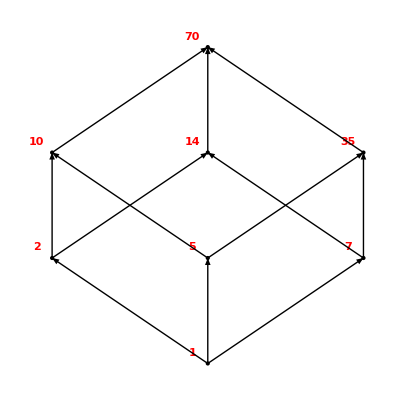

```mathematica
A={1,2,5,7,10,14,35,70};
R={{1,1},{1,2},{1,5},{1,7},{1,10},{1,14},{1,35},{1,70},{2,2},{2,10},{2,14},{2,70},{5,5},{5,10},{5,35},{5,70},{7,7},{7,14},{7,35},{7,70},{10,10},{10,70},{14,14},{14,70},{35,35},{35,70},{70,70}};
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

Por tanto tenemos un retículo isomorfo a (2)3 y en consecuencia es un álgebra de Boole. Es muy fácil definir un isomorfismo entre D y (2)3. Podríamos hacerlo como sigue:

```mathematica
f[1]:={0,0,0};f[2]:={1,0,0};f[5]:={0,1,0};f[7]:={0,0,1};f[10]:={1,1,0};f[14]:={1,0,1};f[35]:={0,1,1};f[70]:={1,1,1};
```

Y usando el programa 7.5.nos comprueba que la aplicación definida previamente es una biyección :

```mathematica
A={1,2,5,7,10,14,35,70};
B={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0},{1,0,1},{0,1,1},{1,1,1}};
f[1]:={0,0,0};f[2]:={1,0,0};f[5]:={0,1,0};f[7]:={0,0,1};f[10]:={1,1,0};f[14]:={1,0,1};f[35]:={0,1,1};f[70]:={1,1,1};
Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[A[[i]]]]],{i,1,Length[A]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[B],Print["Es sobreyectiva"],Print["No es sobreyectiva"]];
If[Length[A]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[A]==Length[B]&&Length[B]==Length[Imagen],Print["Es biyectiva"],Print["No es biyectiva"]];
```

El conjunto imagen es: {{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

Es sobreyectiva

Es inyectiva

Es biyectiva

Podemos obviar la comprobación de la preservación del orden. Observemos que al definir la biyección lo hacemos de manera no aleatoria, sino que se va asignando como imagen de cada elemento de manera que se respeta la estructura de orden del algebra de Boole 𝔹_2^3.

### Ejemplo 9.15.

Dado el conjunto D de todos los divisores positivos de 24 con la relación de orden
R = {(24, 24), (24, 12), (24, 8), (24, 6), (24, 4), (24, 3), (24, 2), (24, 1), (12, 12), (12, 6),    
         (12, 4), (12, 3), (12, 2), (12, 1), (8, 8), (8, 4), (8, 2), (8, 1), (6, 6), (6, 3), (6, 2), (6, 1), 
        (4, 4), (4, 2), (4, 1), (3, 3), (3, 1), (2, 2), (2, 1), (1, 1)}
Vamos a comprobar:
	a)	Si es un conjunto ordenado.
	b)	Si es un retículo.
	c)	El conjunto de sus átomos es M = {12, 8}.
	d)	Si es un álgebra de Boole usando el teorema de estructura de las álgebras de  Boole finitas definiendo una aplicación de D y 𝒫(M).

```mathematica
ORDEN[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

```mathematica
RETICULO[A_,R_]:=Module[{reticulo,cotassuperiores,cotasinferiores,csuper,cinfer,supremo,infimo,mini,maxi,n,m,x1,x2},reticulo=True;
Do[Do[cotassuperiores={};cotasinferiores={};
Do[csuper=True;cinfer=True;
If[Intersection[{{A[[x1]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[x2]],A[[n]]}},R]=={},csuper=False];
If[Intersection[{{A[[n]],A[[x1]]}},R]=={},cinfer=False];
If[Intersection[{{A[[n]],A[[x2]]}},R]=={},cinfer=False];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};infimo={};
Do[mini=True;
Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];
If[supremo=={},reticulo=False];
Do[maxi=True;
Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];
         ,{n,1,Length[cotasinferiores]}];
If[infimo=={},reticulo=False];
      ,{x1,1,Length[A]}];
   ,{x2,1,Length[A]}];
reticulo
]
```

```mathematica
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},
minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales
]
```

```mathematica
A={1,2,3,4,6,8,12,24};
R={{24,24},{24,12},{24,8},{24,6},{24,4},{24,3},{24,2},{24,1},{12,12},{12,6},{12,4},{12,3},{12,2},{12,1},{8,8},{8,4},{8,2},{8,1},{6,6},{6,3},{6,2},{6,1},{4,4},{4,2},{4,1},{3,3},{3,1},{2,2},{2,1},{1,1}};
ORDEN[A,R]
```

R es reflexiva

R es antisimétrica

R es transitiva

R es una relación de orden

```mathematica
RETICULO[A,R]
```

True

```mathematica
MINIMALES[A,R]
```

{24}

Por tanto, el elemento cero es el 24.

```mathematica
MINIMALES[{1,2,3,4,6,8,12},R]
```

{8,12}

Los átomos de este retículo son el 8 y el 12. Lo comprobamos también dibujando su diagrama de Hasse:

Diagrama de orden:

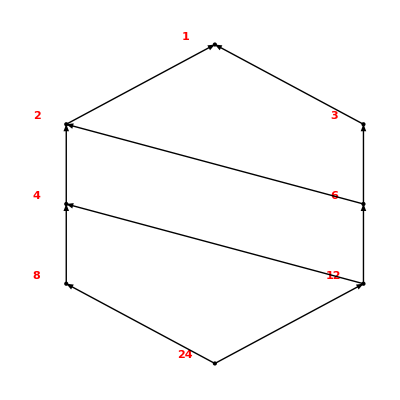

```mathematica
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

De este diagrama podemos deducir que D no se trata de un álgebra de Boole.

### Ejemplo 9.16.

Aplicar la función anterior a partes del conjunto A = {x, y, z, t} con la relación de orden dada por la inclusión y comprobamos que en efecto es álgebra de Boole, también obtenemos el isomorfismo correspondiente con 𝔹_2^n con n = card(A).

```mathematica
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},
maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales
]
```

```mathematica
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},
minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales
]
```

```mathematica
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},
cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};
Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];
supremo
]
```

```mathematica
BOOLE[L_,R_]:=Module[{minimales,cero,preimagen,supremo,i,j,k,l,n,conjunto,imagen,f,nmin},
ABoole=True;minimales=MINIMALES[L,R];
If[Length[minimales]≠1, ABoole=False,
cero=minimales[[1]];minimales=MINIMALES[Complement[L,{cero}],R];
n=Length[minimales];f[cero]:=Table[0,{i,n}];
Do[f[minimales[[i]]]=Table[If[j≠i,0,1],{j,n}];,{i,n}];
ABoole=(Length[L]==(2^n) && Length[R]==Sum[(n!/(k!(n-k)!))*2^(n-k),{k,0,n}]);
If[ABoole,
imagen=Union[{f[cero]},Table[f[minimales[[i]]],{i,Length[minimales]}]];
preimagen=Union[{cero},minimales];
l=2;
While[l≤n && ABoole,
conjunto={};j=1;nmin=Length[minimales];
While[j≤nmin && ABoole,
i=j+1;
While[i≤nmin && ABoole,
If[Length[Position[f[minimales[[i]]]+f[minimales[[j]]],0]]==n-l,
supremo=SUPREMO[L,{minimales[[i]],minimales[[j]]},R][[1]];
If[Intersection[preimagen,{supremo}]=={},
conjunto=Union[conjunto,{supremo}];
f[supremo]=Table[If[(f[minimales[[i]]]+f[minimales[[j]]])[[k]]≠0,1,0],{k,n}];
imagen=Union[imagen,{f[supremo]}];
preimagen=Union[preimagen,{supremo}];
,If[Intersection[{supremo},conjunto]=={},ABoole=False;];
];];i++;];j++;];
minimales=conjunto;
ABoole=(Length[conjunto]==(n!/(l!*(n-l)!)));
l++;];
ABoole=(Length[imagen]==2^n && Length[preimagen]==2^n);
];];
If[ABoole,
Print["Es álgebra de Boole, un isomorfismo con ", Superscript["𝔹_2",n]," viene dado por:"];
Do[Print[L[[i]]," → ",f[L[[i]]]];,{i,2^n}];
,
Print["No es álgebra de Boole"];];
];
```

```mathematica
Clear[x,y,z,t];
```

```mathematica
A=Subsets[{x,y,z,t}];(*Calculamos P(A)*)
n=Length[A];(*Cardinal de A*)

R={};(*Calculamos R*)
Do[Do[
If[Sort[Intersection[A[[j]],A[[i]]]]==Sort[A[[i]]],
AppendTo[R,{A[[i]],A[[j]]}];
];
,{j,1,n}];,{i,1,n}];
```

```mathematica
BOOLE[A,R]
```

Es álgebra de Boole, un isomorfismo con 𝔹_2^4 viene dado por:

{} → {0,0,0,0}

{x} → {0,1,0,0}

{y} → {0,0,1,0}

{z} → {0,0,0,1}

{t} → {1,0,0,0}

{x,y} → {0,1,1,0}

{x,z} → {0,1,0,1}

{x,t} → {1,1,0,0}

{y,z} → {0,0,1,1}

{y,t} → {1,0,1,0}

{z,t} → {1,0,0,1}

{x,y,z} → {0,1,1,1}

{x,y,t} → {1,1,1,0}

{x,z,t} → {1,1,0,1}

{y,z,t} → {1,0,1,1}

{x,y,z,t} → {1,1,1,1}

### Ejemplo 9.17.

Consideremos el conjunto de los divisores positivos del número entero 637 con la relación de orden dada por la divisibilidad. Usar la función 9.6. para comprobar si es un álgebra de Boole.

```mathematica
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},
maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales
]
```

```mathematica
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},
minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales
]
```

```mathematica
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},
cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};
Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];
supremo
]
```

```mathematica
BOOLE[L_,R_]:=Module[{minimales,cero,preimagen,supremo,i,j,k,l,n,conjunto,imagen,f,nmin},
ABoole=True;minimales=MINIMALES[L,R];
If[Length[minimales]≠1, ABoole=False,
cero=minimales[[1]];minimales=MINIMALES[Complement[L,{cero}],R];
n=Length[minimales];f[cero]:=Table[0,{i,n}];
Do[f[minimales[[i]]]=Table[If[j≠i,0,1],{j,n}];,{i,n}];
ABoole=(Length[L]==(2^n) && Length[R]==Sum[(n!/(k!(n-k)!))*2^(n-k),{k,0,n}]);
If[ABoole,
imagen=Union[{f[cero]},Table[f[minimales[[i]]],{i,Length[minimales]}]];
preimagen=Union[{cero},minimales];
l=2;
While[l≤n && ABoole,
conjunto={};j=1;nmin=Length[minimales];
While[j≤nmin && ABoole,
i=j+1;
While[i≤nmin && ABoole,
If[Length[Position[f[minimales[[i]]]+f[minimales[[j]]],0]]==n-l,
supremo=SUPREMO[L,{minimales[[i]],minimales[[j]]},R][[1]];
If[Intersection[preimagen,{supremo}]=={},
conjunto=Union[conjunto,{supremo}];
f[supremo]=Table[If[(f[minimales[[i]]]+f[minimales[[j]]])[[k]]≠0,1,0],{k,n}];
imagen=Union[imagen,{f[supremo]}];
preimagen=Union[preimagen,{supremo}];
,If[Intersection[{supremo},conjunto]=={},ABoole=False;];
];];i++;];j++;];
minimales=conjunto;
ABoole=(Length[conjunto]==(n!/(l!*(n-l)!)));
l++;];
ABoole=(Length[imagen]==2^n && Length[preimagen]==2^n);
];];
If[ABoole,
Print["Es álgebra de Boole, un isomorfismo con ", Superscript["𝔹_2",n]," viene dado por:"];
Do[Print[L[[i]]," → ",f[L[[i]]]];,{i,2^n}];
,
Print["No es álgebra de Boole"];];
];
```

```mathematica
A=Divisors[637];
n=Dimensions[A][[1]];
R={};
Do[Do[If[Mod[A[[j]],A[[i]]]==0,R=Union[R,{{A[[i]],A[[j]]}}]],{i,1,n}],{j,1,n}];
```

```mathematica
BOOLE[A,R]
```

No es álgebra de Boole